```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Lipei/Documents/GitHub/source

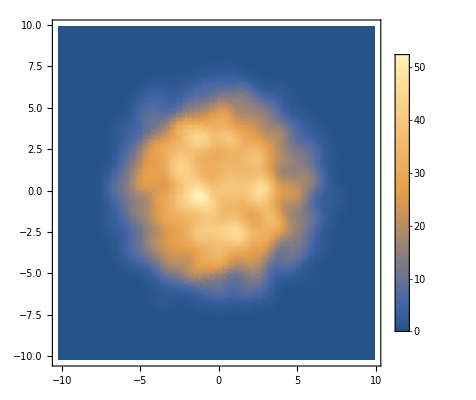

```mathematica
data=Import["output/sources1.dat"];
xy=data[[All,{1,2,4}]];
ListDensityPlot[xy,PlotLegends->Automatic,PlotRange->All]
```

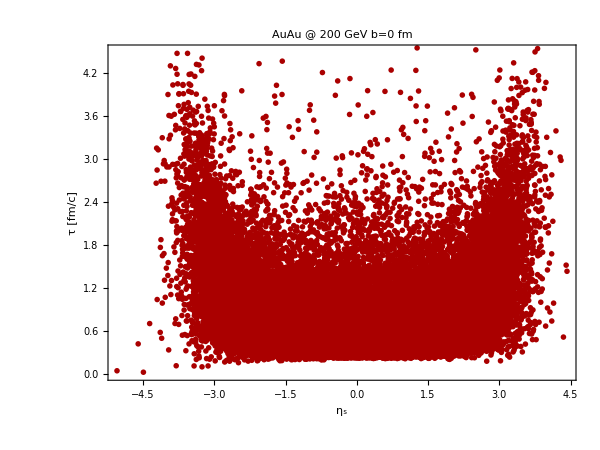

```mathematica
tVSz1=ListPlot[Transpose[Transpose[Import["output/Milne.dat","Table"]][[{4,1}]]],PlotRange->{0,4.5},Frame->True,Axes->False,FrameLabel->{"η_s","τ [fm/c]"},FrameStyle->Directive[AbsoluteThickness[1.1]],BaseStyle->{FontFamily->"Times",FontSize->20},ImageSize->600,AspectRatio->0.75,ImagePadding->{{85,30},{80,20}},PlotStyle->{AbsolutePointSize[4],Darker[Red]},PlotLabel->"AuAu @ 200 GeV b=0 fm"]
```